```mathematica
S[x_]:=Exp[-Abs[x]/2]
Subscript[k, w][x_,ξ_]:=Piecewise[{{1/(2Sqrt[Subscript[β, w]])Exp[Sqrt[Subscript[β, w]](ξ-x)],x>ξ},{1/(2Sqrt[Subscript[β, w]])Exp[Sqrt[Subscript[β, w]](x-ξ)],x<ξ}}]
Subscript[k, l][x_,ξ_]:=Piecewise[{{1/(2Sqrt[Subscript[β, l]])Exp[Sqrt[Subscript[β, l]](ξ-x)],x>ξ},{1/(2Sqrt[Subscript[β, l]])Exp[Sqrt[Subscript[β, l]](x-ξ)],x<ξ}}]
var=Rationalize[{Subscript[α, w]->50.58,Subscript[β, w]->3.85/0.38,Subscript[η, w]->1/(0.38*10)*Q,Subscript[α, l]->192.2/(1.89*10),Subscript[β, l]->3.85/1.89,Subscript[η, l]->1/(1.89*10)*Q,Subscript[a, 0]->0.6,Subscript[a, 1]->0.38,M->0.38/1.89,Subscript[L, 0]->-1+ϵ,Subscript[L, 1]->1+ϵ}];
```

```mathematica
Subscript[T, 0][ξ_]:=Limit[Subscript[c, 0] Subscript[k, w][x,ξ]+D[Subscript[k, w][x,ξ], x],x->Subscript[A, 0],Assumptions->ξ<Subscript[A, 0]]-
Subscript[α, w] Integrate[Subscript[k, w][x,ξ],{x,-∞,Subscript[A, 0]},Assumptions->ξ<Subscript[A, 0]<Subscript[L, 0]/.var]+
Subscript[η, w](1-Subscript[a, 0])Integrate[Subscript[k, w][x,ξ]S[x],{x,-∞,Subscript[A, 0]},Assumptions->ξ<Subscript[A, 0]<Subscript[L, 0]/.var]
Subscript[F, 0][ξ_]=Refine[Subscript[T, 0][ξ]/.var,{0<ϵ<1,ξ<Subscript[A, 0]<0}];
```

```mathematica
Subscript[T, 1][ξ_]:=Limit[Subscript[c, 2] Subscript[k, w][x,ξ]-Subscript[c, 1] D[Subscript[k, w][x,ξ], x],x->Subscript[L, 0],Assumptions->ξ<Subscript[L, 0]]-
Limit[Subscript[c, 0] Subscript[k, w][x,ξ]+ D[Subscript[k, w][x,ξ], x],x->Subscript[A, 0],Assumptions->ξ>Subscript[A, 0]]-
Subscript[α, w] Integrate[Subscript[k, w][x,ξ],{x,Subscript[A, 0],Subscript[L, 0]}/.var,Assumptions->{Subscript[A, 0]<ξ<Subscript[L, 0]/.var,Subscript[A, 0]<Subscript[L, 0]/.var}]+
Subscript[η, w](1-Subscript[a, 1])Integrate[Subscript[k, w][x,ξ]S[x],{x,Subscript[A, 0],Subscript[L, 0]}/.var,Assumptions->{Subscript[A, 0]<ξ<Subscript[L, 0]/.var,Subscript[A, 0]<Subscript[L, 0]/.var}]
Subscript[F, 1][ξ_]=Refine[Subscript[T, 1][ξ]/.var,{0<ϵ<1,Subscript[A, 0]<ξ<Subscript[L, 0]<0}/.var];
```

```mathematica
Subscript[T, 2][ξ_]:=Limit[Subscript[c, 3] Subscript[k, l][x,ξ],x->Subscript[B, 0],Assumptions->ξ<Subscript[B, 0]]-
Limit[M Subscript[c, 2] Subscript[k, l][x,ξ]-Subscript[c, 1] D[Subscript[k, l][x,ξ], x],x->Subscript[L, 0],Assumptions->ξ>Subscript[L, 0]]-
Subscript[α, l] Integrate[Subscript[k, l][x,ξ],{x,Subscript[L, 0],Subscript[B, 0]}/.var,Assumptions->Subscript[B, 0]>Subscript[L, 0]/.var]+
Subscript[η, l](1-Subscript[a, 1])Integrate[Subscript[k, l][x,ξ]S[x],{x,Subscript[L, 0],Subscript[B, 0]}/.var,Assumptions->Subscript[B, 0]>Subscript[L, 0]/.var]
Subscript[F, 2][ξ_]=Refine[Subscript[T, 2][ξ]/.var,{0<ϵ<1,Subscript[L, 0]<ξ<Subscript[B, 0]}/.var];
```

```mathematica
Subscript[T, 3][ξ_]:=Limit[M Subscript[c, 5] Subscript[k, l][x,ξ]- Subscript[c, 4] D[Subscript[k, l][x,ξ], x],x->Subscript[L, 1],Assumptions->ξ<Subscript[L, 1]]-
Limit[Subscript[c, 3] Subscript[k, l][x,ξ],x->Subscript[B, 0],Assumptions->ξ>Subscript[B, 0]]-
Subscript[α, l] Integrate[Subscript[k, l][x,ξ],{x,Subscript[B, 0],Subscript[L, 1]}/.var,Assumptions->Subscript[B, 0]<Subscript[L, 1]/.var]+
Subscript[η, l](1-Subscript[a, 0])Integrate[Subscript[k, l][x,ξ]S[x],{x,Subscript[B, 0],Subscript[L, 1]}/.var,Assumptions->Subscript[B, 0]<Subscript[L, 1]/.var]
Subscript[F, 3][ξ_]=Refine[Subscript[T, 3][ξ]/.var,{0<ϵ<1,Subscript[B, 0]<ξ<Subscript[L, 1]}/.var];
```

```mathematica
Subscript[T, 4][ξ_]:=-Limit[Subscript[c, 5] Subscript[k, w][x,ξ]-Subscript[c, 4] D[Subscript[k, w][x,ξ], x],x->Subscript[L, 1],Assumptions->ξ>Subscript[L, 1]]-
Subscript[α, w] Integrate[Subscript[k, w][x,ξ],{x,Subscript[L, 1],∞}/.var,Assumptions->ξ>Subscript[L, 1]/.var]+
Subscript[η, w](1-Subscript[a, 0])Integrate[Subscript[k, w][x,ξ]S[x],{x,Subscript[L, 1],∞}/.var,Assumptions->ξ>Subscript[L, 1]/.var]
Subscript[F, 4][ξ_]=Refine[Subscript[T, 4][ξ]/.var,{0<ϵ<1,Subscript[L, 1]<ξ}/.var];
```

```mathematica
Subscript[eqn, 0]=Subscript[F, 0][Subscript[A, 0]]+1==0;
Subscript[eqn, 1]=Subscript[F, 1][Subscript[A, 0]]+1==0;
Subscript[eqn, 2]=Subscript[F, 2][Subscript[B, 0]]==0;
Subscript[eqn, 3]=Subscript[F, 3][Subscript[B, 0]]==0;
Subscript[eqn, 4]=Subscript[F, 2]'[Subscript[L, 0]]-M Subscript[F, 1]'[Subscript[L, 0]]==0/.var;
Subscript[eqn, 5]=Subscript[F, 3]'[Subscript[L, 1]]-M Subscript[F, 4]'[Subscript[L, 1]]==0/.var;
Subscript[eqn, 6]=Subscript[F, 2][Subscript[L, 0]]-Subscript[F, 1][Subscript[L, 0]]==0/.var;
Subscript[eqn, 7]=Subscript[F, 3][Subscript[L, 1]]-Subscript[F, 4][Subscript[L, 1]]==0/.var;
```

```mathematica
Beep[]
```

```mathematica
(*Finding what Q's has solution on this form*)
Subscript[Q, min]=485.633531386482;
Subscript[Q, max]=486.1644145500261;
n=Round[6Abs[Subscript[Q, max]-Subscript[Q, min]]+1];
Subscript[ϵ, test]=0.04;
sols={};
Monitor[
For[i=0,i<n,i++,
tempQ={Q->Rationalize[Subscript[Q, min]+(Subscript[Q, max]-Subscript[Q, min])*i/(n-1),0],ϵ->Rationalize[Subscript[ϵ, test],0]};
(*sol=Quiet[FindRoot[{Subscript[eqn, 0],Subscript[eqn, 1],Subscript[eqn, 2],Subscript[eqn, 3],Subscript[eqn, 4],Subscript[eqn, 5],Subscript[eqn, 6],Subscript[eqn, 7]}/.tempQ,{{Subscript[c, 0],0},{Subscript[c, 1],0},{Subscript[c, 2],0},{Subscript[c, 3],0},{Subscript[c, 4],0},{Subscript[c, 5],0},{Subscript[A, 0],-2},{Subscript[B, 0],0.5}},MaxIterations->100,WorkingPrecision->30]];*)
sol=Quiet[FindRoot[{Subscript[eqn, 0],Subscript[eqn, 1],Subscript[eqn, 2],Subscript[eqn, 3],Subscript[eqn, 4],Subscript[eqn, 5],Subscript[eqn, 6],Subscript[eqn, 7]}/.tempQ,{{Subscript[c, 0],Subscript[c, 0]/.sol},{Subscript[c, 1],Subscript[c, 1]/.sol},{Subscript[c, 2],Subscript[c, 2]/.sol},{Subscript[c, 3],Subscript[c, 3]/.sol},{Subscript[c, 4],Subscript[c, 4]/.sol},{Subscript[c, 5],Subscript[c, 5]/.sol},{Subscript[A, 0],Subscript[A, 0]/.sol},{Subscript[B, 0],Subscript[B, 0]/.sol}},MaxIterations->100,WorkingPrecision->30]];
sol=Join[sol,tempQ,var/.tempQ];
Quiet[conds=Subscript[A, 0]<Subscript[L, 0]<Subscript[B, 0]<Subscript[L, 1]&&
NMaxValue[{Subscript[F, 0][x],-10<x<Subscript[A, 0]}/.sol,x]<-0.99999&&
NMinValue[{Subscript[F, 1][x],Subscript[A, 0]<x<Subscript[L, 0]}/.sol,x]>-1.00001&&
NMinValue[{Subscript[F, 2][x],Subscript[L, 0]<x<Subscript[B, 0]}/.sol,x]>-0.00001&&
NMaxValue[{Subscript[F, 3][x],Subscript[B, 0]<x<Subscript[L, 1]}/.sol,x]<0.00001&&
NMaxValue[{Subscript[F, 4][x],Subscript[L, 1]<x<10}/.sol,x]<-0.99999/.sol];
If[conds,M[x_]=Rationalize[Piecewise[{{Subscript[F, 0][x],x<=Subscript[A, 0]},{Subscript[F, 1][x],Subscript[A, 0]<x<Subscript[L, 0]},{Subscript[F, 2][x],Subscript[L, 0]<=x<Subscript[B, 0]},{Subscript[F, 3][x],Subscript[B, 0]<=x<=Subscript[L, 1]},{Subscript[F, 4][x],Subscript[L, 1]<x}}/.sol],0];
NUM=12001;
points=SetPrecision[Table[-6+12(i-1)/(NUM-1),{i,NUM}],20];
nSolution=N[Map[M, points]];
sols=Join[sols,{{N[Q/.sol],N[M[0]/.sol],N[M[ϵ]/.sol],nSolution}}],Nothing];
],{N[i/n],N[Q/.tempQ]}]
Beep[]
```

```mathematica
Export["C:\\masterA GitHub\\Code\\Exponential\\Continent Offset 0.000\\5C - IceWaterLandSnowIce.csv",sols,Format->Table];
```

```mathematica
Subscript[Q, min]=485.633531386482;
Subscript[Q, max]=486.1644145500261;
n=Round[6Abs[Subscript[Q, max]-Subscript[Q, min]]+1]
```

4

```mathematica
485.633531386482
```

```mathematica
486.1644145500261
```

{c_0→4.97528139322900680734124833269,c_1→0.0147665277546616971022786169359,c_2→4.77492953134908278282890238625,c_3→-2.06659421398780868275591031285,c_4→-1.00000000000000593308890106595,c_5→-4.4467666636181691466341447853,A_0→-1.17223366403796739634667660597,B_0→0.373749332920564421864986663996}

-0.0233387 | -0.962638

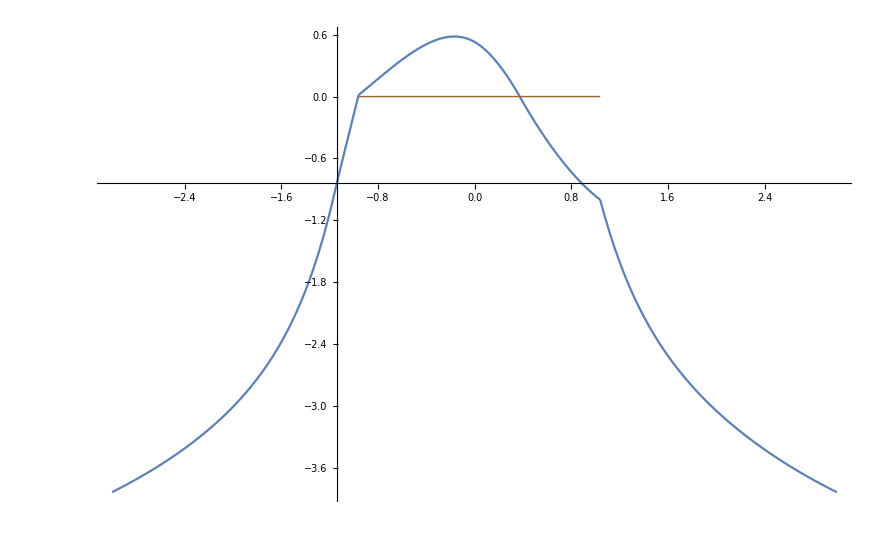

```mathematica
(* Finding particular solution *)
tempQ={Q->Rationalize[486.1644145500261,0],ϵ->Rationalize[0.04,0]};
usePrev=True;
If[usePrev,sol=FindRoot[{Subscript[eqn, 0],Subscript[eqn, 1],Subscript[eqn, 2],Subscript[eqn, 3],Subscript[eqn, 4],Subscript[eqn, 5],Subscript[eqn, 6],Subscript[eqn, 7]}/.tempQ,{{Subscript[c, 0],Subscript[c, 0]/.sol},{Subscript[c, 1],Subscript[c, 1]/.sol},{Subscript[c, 2],Subscript[c, 2]/.sol},{Subscript[c, 3],Subscript[c, 3]/.sol},{Subscript[c, 4],Subscript[c, 4]/.sol},{Subscript[c, 5],Subscript[c, 5]/.sol},{Subscript[A, 0],Subscript[A, 0]/.sol},{Subscript[B, 0],Subscript[B, 0]/.sol}},MaxIterations->100,WorkingPrecision->30],
sol=FindRoot[{Subscript[eqn, 0],Subscript[eqn, 1],Subscript[eqn, 2],Subscript[eqn, 3],Subscript[eqn, 4],Subscript[eqn, 5],Subscript[eqn, 6],Subscript[eqn, 7]}/.tempQ,{{Subscript[c, 0],0},{Subscript[c, 1],0},{Subscript[c, 2],0},{Subscript[c, 3],0},{Subscript[c, 4],0},{Subscript[c, 5],0},{Subscript[A, 0],-1.17},{Subscript[B, 0],-0.9}},MaxIterations->100,WorkingPrecision->30]]
sol=Join[Rationalize[sol,0],tempQ,var/.tempQ];
(* Plotting solution *)
Subscript[p, 0]=Plot[Subscript[F, 0][x]/.sol,{x,-3,Subscript[A, 0]}/.sol,PlotRange->All,WorkingPrecision->20];
Subscript[p, 1]=Plot[Subscript[F, 1][x]/.sol,{x,Subscript[A, 0],Subscript[L, 0]}/.sol,PlotRange->All,WorkingPrecision->20];
Subscript[p, 2]=Plot[Subscript[F, 2][x]/.sol,{x,Subscript[L, 0],Subscript[B, 0]}/.sol,PlotRange->All,WorkingPrecision->20];
Subscript[p, 3]=Plot[Subscript[F, 3][x]/.sol,{x,Subscript[B, 0],Subscript[L, 1]}/.sol,PlotRange->All,WorkingPrecision->20];
Subscript[p, 4]=Plot[Subscript[F, 4][x]/.sol,{x,Subscript[L, 1],3}/.sol,PlotRange->All,WorkingPrecision->20];
Subscript[p, 5]=Plot[0,{x,Subscript[L, 0],Subscript[L, 1]}/.sol,PlotRange->All,PlotStyle->{Brown,Thick}];
Print[N[Subscript[F, 2][-1]]/.sol," | ",N[Subscript[F, 3][1]]/.sol]
Show[Subscript[p, 0],Subscript[p, 1],Subscript[p, 2],Subscript[p, 3],Subscript[p, 4],Subscript[p, 5],PlotRange->All]
```

```mathematica
sol=FindRoot[{Subscript[eqn, 0],Subscript[eqn, 1],Subscript[eqn, 2],Subscript[eqn, 3],Subscript[eqn, 4],Subscript[eqn, 5],Subscript[eqn, 6],Subscript[eqn, 7],Subscript[c, 4]==-1}/.{ϵ->0.04},{{Subscript[c, 0],0},{Subscript[c, 1],0},{Subscript[c, 2],0},{Subscript[c, 3],0},{Subscript[c, 4],0},{Subscript[c, 5],0},{Subscript[A, 0],-1.17},{Subscript[B, 0],0.4},{Q,486}},MaxIterations->100,WorkingPrecision->30]
```

FindRoot::precw: The precision of the argument function (…) is less than WorkingPrecision (30.).

{c_0→4.97528139322900710283553227754,c_1→0.014766527754665189661623111884,c_2→4.77492953134908481253166306043,c_3→-2.06659421398781236209857568328,c_4→-1.,c_5→-4.44676666361818336314790370036,A_0→-1.17223366403796807493077031433,B_0→0.373749332920569591242986249536,Q→486.164414550026223512723516766}